Differential Equation and Chaos Theory
Tianyi Wang, Wolfram High School Summer Camp 2019

Differential equations are widely used in math, physics, and engineering. These equations are very useful in modelling complex systems that are changing with time. For this exploration, the differential equations we are looking at have a particular form: x’’[t]+x’[t]==f[x[t]], where f is a real-valued function. The solutions exhibit a variety of different behaviors, some of which are stable, others chaotic. The goal of this project is to investigate different chaotic behaviors of these equations and to be able to detect them. Using supervised machine learning, we were able to classify different chaotic behaviors of differential equations.

## 1.Phase Portrait Visualization

-Graphics3D-

The phase portrait visualizes the differential equation in 3D space. For this example, it is rotating around a specific point and finally converges, also evidenced by the following plot:

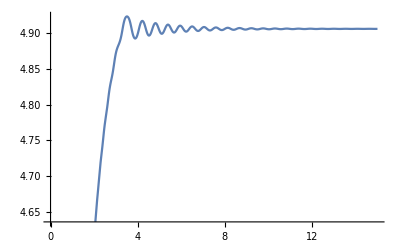

## 3.Euclidean Distance Test

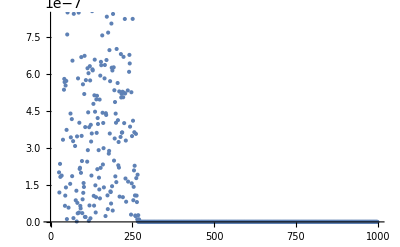

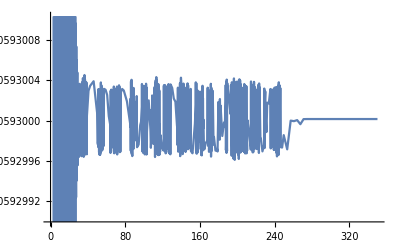

## 4.Behavior Classification

Pictures ( f )

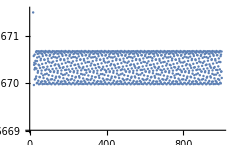
1--Graphics-Sin[x[t]]+1.2 x[t]

2--Graphics-Tan[x[t]]

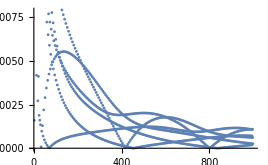
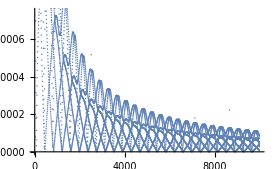
3--Graphics--Graphics-ⅇ^Cos[x[t]]

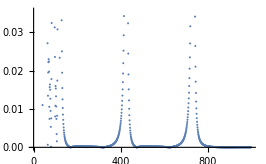
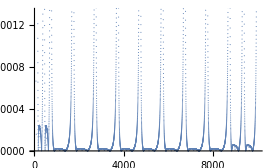
4--Graphics--Graphics--2x[t]

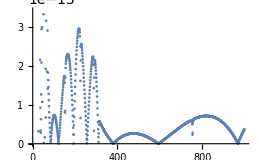
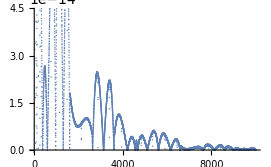
5--Graphics--Graphics-(-1000+x[t]) x[t]^x[t]

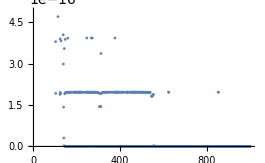
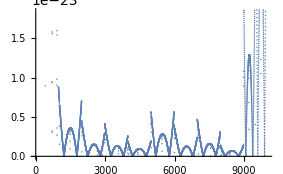
6--Graphics--Graphics-Cos[x[t]^2]

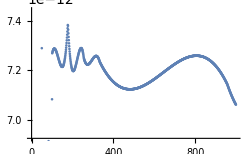
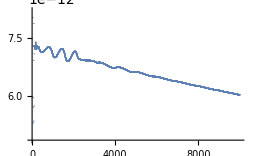
7--Graphics--Graphics-0.287301^(2 x[t])

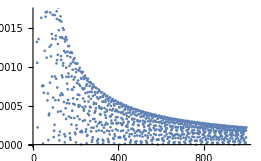
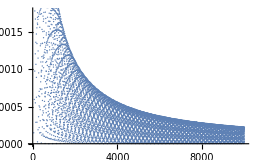
8--Graphics--Graphics-Cos[Sin[x[t]]]

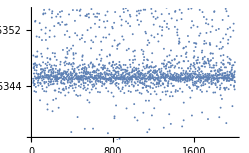
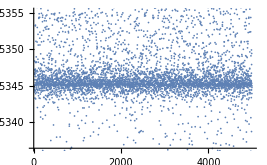
9--Graphics--Graphics-0.0854684 x[t]

## 5.Machine Learning

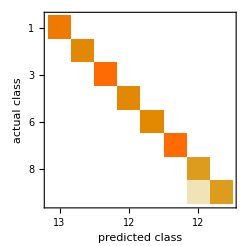
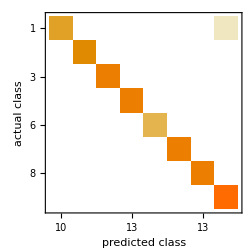
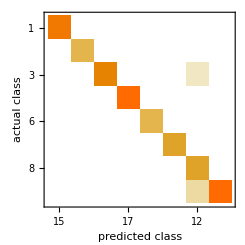

## 6.Conclusion

Throughout this project, I successfully detected the chaotic behavior of different differential equations and classified them. The output includes a function that generates the phase portrait of some differential equations, and a function that tells the interval(s) in which the function is chaotic, for input functions (f[x]) that are continuous. Finally, there is a machine learned classifier function that can classify different behaviors of chaotic functions with accuracy about 99%-100%.